# Manipulate

## Basic Exercises

### Question Subsection

Make a widget that plots the function f(x) = x^n, where n is an integer ranging from 1 to 10.

#### Solution

```mathematica
Manipulate[
Plot[x^n,{x,-5,5},PlotRange->{{-5,5},{-5,5}},PlotStyle->{Thick,Red}],
{n,1,10,1}
]
```

### Question Subsection

Make this cool car go from 0 to 10 using a slider.

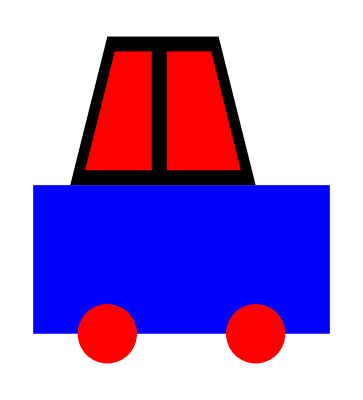

```mathematica
Graphics[{
{Blue,Polygon[{{0,0.2},{2,0.2},{2,1.2},{0,1.2}}]},
{Polygon[{{.25,1.2},{1.5,1.2},{1.25,2.2},{0.5,2.2}}]},
{Red,Polygon[{{0.35,1.3},{.8,1.3},{0.8,2.1},{.55,2.1}}]},
{Red,Polygon[{{0.9,1.3},{1.4,1.3},{1.2,2.1},{.9,2.1}}]},
{Red, Disk[{0.5,0.2},.2]},
{Red, Disk[{1.5,0.2},.2]}
},ImageSize->Tiny]
```

#### Solution

```mathematica
Manipulate[
Graphics[{
{Blue,Polygon[{{x+0,0.2},{x+2,0.2},{x+2,1.2},{x+0,1.2}}]},
{Polygon[{{x+.25,1.2},{x+1.5,1.2},{x+1.25,2.2},{x+0.5,2.2}}]},
{Red,Polygon[{{x+0.35,1.3},{x+.8,1.3},{x+0.8,2.1},{x+.55,2.1}}]},
{Red,Polygon[{{x+0.9,1.3},{x+1.4,1.3},{x+1.2,2.1},{x+.9,2.1}}]},
{Red, Disk[{x+0.5,0.2},.2]},
{Red, Disk[{x+1.5,0.2},.2]},
{Line[{{0,0},{12,0}}]}
}],
{{x,0,"Position"},0,10}
]
```

### Question Subsection

Use Manipulate to give the user the option to change the colors of the windows, body, and the wheels of the car above. You can choose what colors you want to make available to the user.

#### Solution

```mathematica
Manipulate[
Graphics[{
{bodyColor,Polygon[{{0,0.2},{2,0.2},{2,1.2},{0,1.2}}]},
{Polygon[{{.25,1.2},{1.5,1.2},{1.25,2.2},{0.5,2.2}}]},
{windowColor,Polygon[{{0.35,1.3},{.8,1.3},{0.8,2.1},{.55,2.1}}]},
{windowColor,Polygon[{{0.9,1.3},{1.4,1.3},{1.2,2.1},{.9,2.1}}]},
{wheelColor, Disk[{0.5,0.2},.2]},
{wheelColor, Disk[{1.5,0.2},.2]}
},ImageSize->Medium],
{{bodyColor,Blue,"Body Color"},{Blue,Red,Yellow,RGBColor[0.7,0.6,.9]}},
{{windowColor,Red,"Body Color"},{Blue,Red,Yellow,RGBColor[0.7,0.6,.9]}},
{{wheelColor,Black,"Body Color"},{Black,Red,Yellow,RGBColor[0.7,0.4,.8,0.9]}}
]
```